```mathematica
list = Import[NotebookDirectory[]<>"/res/out_0.0.txt","Table"];
Length[list]
len=Length[list[[1]]]
```

20

200

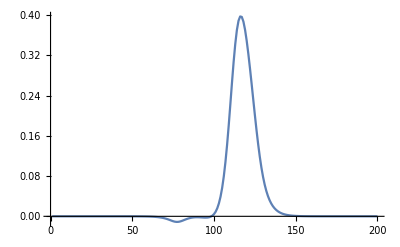

```mathematica
ListLinePlot[-list[[6]],PlotRange->All]
```

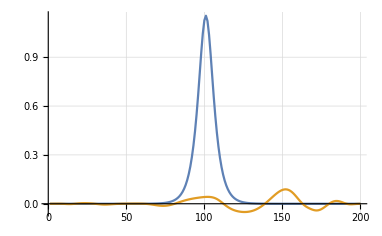

```mathematica
c1=-list[[1]][[1]];
c2=-list[[1]][[1]];
ListLinePlot[{-list[[1]]-c,-list[[-1]]-c},PlotRange->Full,GridLines->Automatic]
```

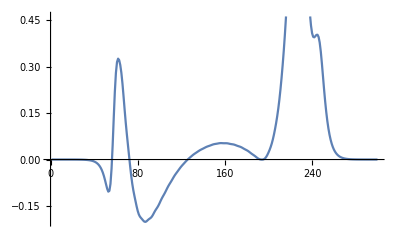

```mathematica
ListLinePlot[ll[[-1]]-ll[[-1,1]]]
```

```mathematica
ll=-list2;
len=Length[ll[[1]]];
f1=NIntegrate[Interpolation[(ll[[1]]-ll[[1,1]])^2,InterpolationOrder->2][x],{x,1,len-1}]
f2=NIntegrate[Interpolation[(ll[[-1]]-ll[[-1,1]])^2,InterpolationOrder->2][x],{x,1,len-1}]
(f1-f2)/f1
```

11.5441

0.00389528

0.999663

```mathematica
list1 = Import[NotebookDirectory[]<>"/res/out_0.0.txt","Table"];
list2 = Import[NotebookDirectory[]<>"/res/out_1.0.txt","Table"];
max=Max[Max[Map[Max,-list1]],Max[Map[Max,-list2]]];
min=Min[Min[Map[Min,-list1]],Min[Map[Min,-list2]]];
```

```mathematica
Manipulate[
l1=-list1[[n]] + list1[[n,1]];
l2=-list2[[n]] + list2[[n,1]];
ListLinePlot[{l1,l2},PlotRange->{min,max}],
{n,1,Length[list2],1}]
```